```mathematica
(* Computer Graphics with Applications of Dr. Makhanov. (Google's Version) *)
```

```mathematica
(*  Lecture 9. Modules Interpolation-2,  Approximation. *)
```

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,ContourPlot3D, DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,ListLinePlot,ListPointPlot3D,Graphics,Graphics3D,PolarPlot}, ImageSize->Medium,AxesLabel->{"x","y","z"}];
```

```mathematica
(* Modules  *)
```

```mathematica
(* f[Input_]:=Module[{x,y,…},expr1; expr2; Output] specifies 
a compound function which returns the Output. The occurrences of the symbols x,y, in expr are treated as the local variables *)
```

```mathematica
(* Example 01 a module to add a+b+Sin[a b] *)
```

```mathematica
Clear[f0]
```

```mathematica
f0[a_,b_]:=Module[{s}, s=a+b;s+=Sin[a b];s]
```

```mathematica
f0[1,Pi/2]
```

2+π/2

```mathematica
(* Example 02 Output a Table of integers from 1 to N *)
```

```mathematica
Clear[f1]
```

```mathematica
f1[N_]:=Module[{T}, T=Table [i,{i,N}];T]
```

```mathematica
f1[100]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
(* Example 03 Output a Table of integers from 1 to N  and the sum of those integers *)
```

```mathematica
Clear[f2]
```

```mathematica
f2[N_]:=Module[{T,S}, T=Table [i,{i,N}];S=Sum[T[[i]],{i,N}];{T,S}]
```

```mathematica
f2[5]
```

{{1,2,3,4,5},15}

```mathematica
(* Example 04 Output a dynamic variable with a slider  *)
```

```mathematica
{Slider[Dynamic[x],{0,1}],Dynamic[x]}
```

{,}

```mathematica
Clear[f3]
```

```mathematica
f3[x_ ]:=Module[{S},S={Slider[Dynamic[x],{0,1}],Dynamic[x]};S]
```

```mathematica
f3[abcd]
```

{,}

```mathematica
Dynamic[abcd]
```

```mathematica
(*  Example 05 Set up a color and return a plot of f[x] *)
```

```mathematica
myPlot[f_,color_]:=Module[{P},P=Plot[f[x],{x,-2Pi,2Pi},PlotStyle->color];P]
```

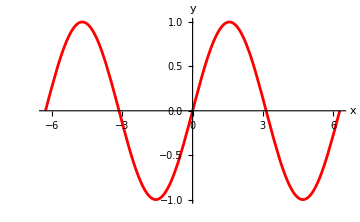

```mathematica
myPlot[Sin,Red]
```

```mathematica
(*  Example 06 Return a function g3=g1+g2  *)
```

```mathematica
myFun[f1_,f2_]:=Module[{f3, t},f3[t_]:=f1[t]+f2[t];f3]
```

```mathematica
Clear[g1];
```

```mathematica
g1[x_]:=x^2; g2[x_]:=Sin[x];
```

```mathematica
g3=myFun[g1,g2];
```

```mathematica
(*  The use of Modules for interpolating curves is demonstrated in the upcoming sections  *)
```

```mathematica
(* Example 1 Recall the 3D example from L8. The curve s4 is interpolated using 3D points given by data 4. 
The solution is given below  *)
```

```mathematica
data4:={{-4,2,4},{4,5,-1},{2,5,0},{1,1,3},{2,-6,-6},{4,4,4}}
```

```mathematica
MatrixForm[data4]
```

(-4 | 2 | 4
4 | 5 | -1
2 | 5 | 0
1 | 1 | 3
2 | -6 | -6
4 | 4 | 4)

```mathematica
x4=Transpose[data4][[1]];
```

```mathematica
y4=Transpose[data4][[2]];
```

```mathematica
z4=Transpose[data4][[3]];
```

```mathematica
sx4=Interpolation[x4,Method->"Spline"];
```

```mathematica
sy4=Interpolation[y4,Method->"Spline"];
```

```mathematica
sz4=Interpolation[z4,Method->"Spline"];
```

```mathematica
(* 3D parametric function, using  the immediate evaluation "=" (discuss) *)
```

```mathematica
s4[t_]={sx4[t],sy4[t],sz4[t]};
```

```mathematica
L0=Length[x4];
```

```mathematica
plot4=ParametricPlot3D[s4[t],{t,1,L0},PlotStyle->{Red, Thickness[0.02]}];
```

```mathematica
plot4points=ListPointPlot3D[data4,PlotStyle->{PointSize[0.07],Blue}];
```

```mathematica
Show[{plot4,plot4points}]
```

-Graphics3D-

```mathematica
(*  The Octahedron is one of the five famous Platonic Solids, see L8 *)
```

```mathematica
{Fire=Graphics3D[{Red,Tetrahedron[]}],Graphics3D[{Yellow,Octahedron[]}],Earth=Graphics3D[{Green,Icosahedron[]}], Water=Graphics3D[{Blue,Icosahedron[]}],Aether=Graphics3D[{Brown,Dodecahedron[]}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
MoveOctahedron[P_]:=Graphics3D[{Yellow,Opacity[0.8],Octahedron[P,2]}, Axes->True, PlotLabel->"Octahedron"]
```

```mathematica
MoveOAlongs4[t_]:= MoveOctahedron[s4[t]]
```

```mathematica
ShowAlls4[t_]:=Show[{plot4,MoveOAlongs4[t]},PlotRange->7]
```

```mathematica
Manipulate[ShowAlls4[t],{t,1,Length[data4]}]
```

```mathematica
(* Solution using modules  *)
```

```mathematica
(* Extract x,y,z from the data  *)
```

```mathematica
Extractxyz[data_]:=Module[{dataT,px,py,pz},
dataT=Transpose[data];
px=dataT[[1]];
py=dataT[[2]];
pz=dataT[[3]];
{px,py,pz}(*output=x,y,z*)]
```

```mathematica
{px,py,pz}=Extractxyz[data4]
```

{{-4,4,2,1,2,4},{2,5,5,1,-6,4},{4,-1,0,3,-6,4}}

```mathematica
(* Generate tx,ty,tz to compose a parametric function s4[s]  *)
```

```mathematica
Interpxyz[data_]:=Module[{px,py,pz,fx,fy,fz},
{px,py,pz}=Extractxyz[data]; 
fx=Interpolation[px];fy=Interpolation[py];fz=Interpolation[pz];{fx,fy,fz}](*output=3 interpolating functions*)
```

```mathematica
{tx,ty,tz}=Interpxyz[data4];
```

```mathematica
s4[t_]:={tx[t],ty[t],tz[t]}
```

```mathematica
(* Plot the interpolating curve  *)
```

```mathematica
plotCurve[data_]:=Module[{t,plot,ss,dx,dy,dz,L0},{dx,dy,dz}=Interpxyz[data];ss[t_]={dx[t],dy[t],dz[t]};L0=Length[data];plot=ParametricPlot3D[ss[t],{t,1,L0},PlotStyle->Red];plot]
```

```mathematica
(* Plot the data and the curve *)
```

```mathematica
plotCurveData[data_]:=Module[{plotcurve,plotdata,show},plotcurve:=plotCurve[data];plotdata:=ListPointPlot3D[data,PlotStyle->{PointSize[0.04],Blue}];show=Show[plotcurve,plotdata];show]
```

```mathematica
P1new=plotCurveData[data4]
```

-Graphics3D-

```mathematica
ShowAllNew[t_]:=Show[{P1new,MoveOAlongs4[t]},PlotRange->7]
```

```mathematica
Manipulate[ShowAllNew[t],{t,1,Length[data4]}]
```

```mathematica
(* Now displaying the curve to interpolate a data takes a few lines *)
```

```mathematica
data5={{0,0,-3},{1,1,1},{2,2,2},{0,0,3},{3,0,0}};
```

```mathematica
P2new= plotCurveData[data5]
```

-Graphics3D-

```mathematica
(* Animation requires extra coding since we need to return 
the coordinates of the curve into the function displaying the object 
i.e. MoveOctahedron[Snew[t]]  *)
```

```mathematica
{newx,newy,newz}=Interpxyz[data5];
```

```mathematica
Snew[t_]:={newx[t],newy[t],newz[t]};
```

```mathematica
MoveOAlongSnew[t_]:= MoveOctahedron[Snew[t]]
```

```mathematica
ShowAllSnew[t_]:=Show[{P2new,MoveOAlongSnew[t]},PlotRange->4]
```

```mathematica
Manipulate[ShowAllSnew[t],{t,1,Length[data5]}]
```

```mathematica
(* Example 2 It is important to understand the difference between animations of the graphic primitives 
such as Cuboid or Circle of Sphere and the ones involving explicit or parametric curves and surfaces. 
Let us move a "handkerchief surface" given by s0[u_,v_]:= {u,v,u^3/3+u v^2+2 (u^2-v^2)} {u,-1,1} {v,-1,1} along the trajectory s4[t]  *)
```

```mathematica
x0[u_,v_]:=u; y0[u_,v_]:=v;z0[u_,v_]:=u^3/3+u v^2+2 (u^2-v^2); s0[u_,v_]:={x0[u,v], y0[u,v],z0[u,v]}
```

```mathematica
G0=ParametricPlot3D[s0[u,v],{u,-1,1},{v,-1,1},BoxRatios->1]
```

-Graphics3D-

```mathematica
(* The origin *)
```

```mathematica
Zero=Graphics3D[{Red,PointSize[0.08],Point[{{0,0,0}}]}];
```

```mathematica
Show[G0,Zero]
```

-Graphics3D-

```mathematica
(* The trajectory is s4[t]  *)
```

```mathematica
plot0t=ParametricPlot3D[s4[t],{t,1,L0},PlotStyle->{Red, Thickness[0.02]}];
```

```mathematica
plot0tpoints=ListPointPlot3D[data4,PlotStyle->{PointSize[0.06],Blue}];
```

```mathematica
GTraj0=Show[{plot0t,plot0tpoints}]
```

-Graphics3D-

```mathematica
(* Adding s4 translates the objects along the trajectory.  *)
```

```mathematica
SurfacePosition0[u_,v_,s_]:=s0[u,v]+s4[s]
```

```mathematica
(* Include color as the animation parameter  *)
```

```mathematica
plots0[s_,color_]:=ParametricPlot3D[SurfacePosition0[u,v,s],{u,-1,1},{v,-1,1},PlotRange->10,
PlotStyle->color]
```

```mathematica
plotShow0[s_,color_]:=Show[plots0[s,color],GTraj0]
```

```mathematica
ColorList0={Red,Green, Blue,Purple,Yellow,Green,Orange,Black,Gray}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0.5, 0, 0.5],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0.5, 0],GrayLevel[0],GrayLevel[0.5]}

```mathematica
Manipulate[plotShow0[s,C],{s,1,L0,0.1},{C,ColorList0}]
```

```mathematica
(*  Interpolation of the surfaces *)
```

```mathematica
(* Interpolate a 3D data given by the heights of the explicit function z=f(x,y) using the synthetic data
data1=Table[Round[Sin[x y],0.1],{x,-1,1,.25},{y,-1,0.75,.25}]
Move the resulting surface along a line L1 through points pp1={-1,-1,-1} and pp2={1,1,1} 
Note that we use  ListInterpolation[data,{{xmin,xmax,{ymin,ymax}}](exp. in class)
*)
```

```mathematica
xmin1=-1;xmax1=1;ymin1=-1;ymax1=0.75;
```

```mathematica
stepx1=0.25;stepy1=stepx1;
```

```mathematica
data1=Table[Round [Sin[x y],0.001]+RandomReal[{-0.25,0.25}],{x,xmin1,xmax1,stepx1},{y,ymin1,ymax1,stepy1}];
```

```mathematica
(* The matrix data1 is synthetic. Our way of getting the data is purely optional  *)
```

```mathematica
MatrixForm[data1]
```

(0.840924 | 0.735174 | 0.70592 | 0.0244387 | 0.208139 | -0.198151 | -0.336657 | -0.602556
0.832569 | 0.411227 | 0.351523 | 0.434655 | -0.111216 | 0.0408236 | -0.507654 | -0.383801
0.376362 | 0.485302 | 0.135941 | 0.247514 | 0.247012 | 0.121098 | -0.119505 | -0.209945
0.36104 | 0.219969 | 0.30198 | 0.269213 | -0.166289 | -0.296485 | -0.0842279 | -0.224648
0.137321 | -0.041006 | 0.1868 | 0.197458 | 0.0000768723 | 0.0967783 | 0.0167608 | 0.123019
-0.224983 | -0.0542066 | -0.104735 | -0.0754114 | 0.086842 | 0.0856157 | 0.306275 | 0.305499
-0.549811 | -0.248095 | -0.312246 | 0.0999276 | -0.0431876 | 0.347818 | 0.250031 | 0.419939
-0.643604 | -0.777185 | -0.565099 | -0.304187 | 0.169638 | 0.307729 | 0.428904 | 0.342268
-0.915133 | -0.769494 | -0.447683 | -0.111014 | -0.0643105 | 0.199295 | 0.542882 | 0.627377)

```mathematica
(* x-range *)
```

```mathematica
DR1={{xmin1,xmax1},{ymin1,ymax1}};
```

```mathematica
GD1=ListPointPlot3D[data1,PlotStyle->PointSize[0.05],DataRange->DR1]
```

-Graphics3D-

```mathematica
Tdata1=Transpose[data1];
```

```mathematica
(* Transpose the matrix to comply with the way the ListInterpolation shows the data *)
```

```mathematica
MatrixForm[Tdata1]
```

(0.840924 | 0.832569 | 0.376362 | 0.36104 | 0.137321 | -0.224983 | -0.549811 | -0.643604 | -0.915133
0.735174 | 0.411227 | 0.485302 | 0.219969 | -0.041006 | -0.0542066 | -0.248095 | -0.777185 | -0.769494
0.70592 | 0.351523 | 0.135941 | 0.30198 | 0.1868 | -0.104735 | -0.312246 | -0.565099 | -0.447683
0.0244387 | 0.434655 | 0.247514 | 0.269213 | 0.197458 | -0.0754114 | 0.0999276 | -0.304187 | -0.111014
0.208139 | -0.111216 | 0.247012 | -0.166289 | 0.0000768723 | 0.086842 | -0.0431876 | 0.169638 | -0.0643105
-0.198151 | 0.0408236 | 0.121098 | -0.296485 | 0.0967783 | 0.0856157 | 0.347818 | 0.307729 | 0.199295
-0.336657 | -0.507654 | -0.119505 | -0.0842279 | 0.0167608 | 0.306275 | 0.250031 | 0.428904 | 0.542882
-0.602556 | -0.383801 | -0.209945 | -0.224648 | 0.123019 | 0.305499 | 0.419939 | 0.342268 | 0.627377)

```mathematica
f1=ListInterpolation[Tdata1,DR1]
```

InterpolatingFunction[…]

```mathematica
(* Plot the surface *)
```

```mathematica
G1inter=Plot3D[f1[x,y],{x,xmin1,xmax1},{y,ymin1,ymax1},PlotStyle->Opacity[0.7],PlotRange->1,BoxRatios->1]
```

-Graphics3D-

```mathematica
(* Superimpose  *)
```

```mathematica
SG10=Show[{G1inter,Zero,GD1},Boxed->True]
```

-Graphics3D-

```mathematica
(* Move the surface along a line through pp1 pp2   *)
```

```mathematica
pp1=-{1,1,1};pp2=-pp1;
```

```mathematica
L1[t_]:=pp1 (1-t)+pp2 t;
```

```mathematica
LT=2;
```

```mathematica
GL1=ParametricPlot3D[L1[t],{t,0,LT},PlotStyle->Purple]
```

-Graphics3D-

```mathematica
(* The line and the surface  *)
```

```mathematica
SG11=Show[SG10,GL1]
```

-Graphics3D-

```mathematica
(* Convert the surface into the parametric form  *)
```

```mathematica
S1[u_,v_]:={u,v,f1[u,v]}
```

```mathematica
Show[G1inter,GL1,Zero]
```

-Graphics3D-

```mathematica
SurfacePosition1[u_,v_,t_]:=S1[u,v]+L1[t]
```

```mathematica
PlotS1[t_]:=ParametricPlot3D[SurfacePosition1[u,v,t],{u,xmin1,xmax1},{v,ymin1,ymax1}]
```

```mathematica
GShowAll[t_]:=Show[{GL1,PlotS1[t],Zero},PlotRange->2]
```

```mathematica
Manipulate[GShowAll[t],{t,0,LT}]
```

```mathematica
(*  Replace the line by the curve ( if time allows) s4[t] *)
```

```mathematica
plot0tpointsNew=ListPointPlot3D[data4,PlotStyle->{PointSize[0.03],Blue}];
```

```mathematica
(*  The surface is too small. Hence, the size has been tripled *)
```

```mathematica
S1New[u_,v_]:=3*S1[u,v]
```

```mathematica
SurfacePositionNew[u_,v_,t_]:=S1New[u,v]+s4[t]
```

```mathematica
plotNew[s_,color_]:=ParametricPlot3D[SurfacePositionNew[u,v,s],{u,-1,1},{v,-1,1},PlotRange->8,
PlotStyle->color]
```

```mathematica
GTrajNew=P1new
```

-Graphics3D-

```mathematica
plotShowNew[s_,color_]:=Show[plotNew[s,color],GTrajNew]
```

```mathematica
ColorListNew=RandomColor[8]
```

{RGBColor[0.7936712297272353, 0.5586832744655956, 0.16463790562691005],RGBColor[0.9713610531922738, 0.6841268346695122, 0.4416286609167297],RGBColor[0.19305563950532112, 0.9390931258213642, 0.24423070208981001],RGBColor[0.7358137435434708, 0.8514518004266804, 0.25404325349601753],RGBColor[0.4826684081358099, 0.21971835663595174, 0.5121237308515383],RGBColor[0.2796386703204905, 0.9983430717878563, 0.9982317965118139],RGBColor[0.7345178734968005, 0.4823571987114612, 0.4761061121587351],RGBColor[0.7791836896004121, 0.14523000517803264, 0.1508559122503097]}

```mathematica
Manipulate[plotShowNew[s,C],{s,1,L0,0.1},{C,ColorListNew}]
```

```mathematica
(*  Approximation *)
```

```mathematica
(*-Graphics-*)
```

```mathematica
(* Polynomial fit  *)
```

```mathematica
(* Find which polynomial quadratic, cubic or the 4-th degree is the best to fit the synthetic data given by    *)
```

```mathematica
Ra=Table[RandomReal[{-0.1,0.1}],{i,20}];
```

```mathematica
(* Ra has been fixed here *)
```

```mathematica
Ra={-0.05236238931852946,0.08359494704236292,-0.053550839328352,-0.04634513261359163,0.08799040242653361,-0.05101500058865194,-0.06876704395496874,0.07665735756773517,0.08846985110414324,-0.03537372218433482,-0.03710776367124763,-0.04383343506482473,-0.0033938052553045828,0.01169277191086543,-0.08308991585530359,-0.03388099605477596,0.07789191692608466,-0.0848502619397723,0.08068710512497868,-0.010080357863596179};
```

```mathematica
data2 = Table[{x/20,Cos[x^2]}+Ra[[x]],{x,20}];
```

```mathematica
data2
```

{{-0.00236239,0.48794},{0.183595,-0.570049},{0.0964492,-0.964681},{0.153655,-1.004},{0.33799,1.07919},{0.248985,-0.178979},{0.281233,0.231825},{0.476657,0.468515},{0.53847,0.865156},{0.464626,0.826945},{0.512892,-0.0857714},{0.556167,0.827314},{0.646606,0.795102},{0.711693,0.354159},{0.66691,0.284229},{0.766119,-0.0736718},{0.927892,1.07754},{0.81515,-0.99958},{1.03069,-0.879492},{0.98992,-0.535377}}

```mathematica
D2=Transpose[data2];
```

```mathematica
xmin2=Min[D2[[1]]];
```

```mathematica
xmax2=Max[D2[[1]]];
```

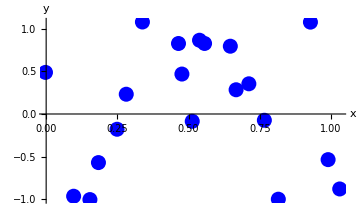

```mathematica
Gdata2=ListPlot[data2, PlotStyle->{Blue, PointSize[0.03]}]
```

```mathematica
(* Set up the basis functions as follows *)
```

```mathematica
Clear[x,t]
```

```mathematica
bf2={x,x^2}
```

{x,x^2}

```mathematica
p2=LinearModelFit[data2,bf2,x];
```

```mathematica
p2[t]
```

-0.670232+4.17593 t-3.91989 t^2

```mathematica
bf3={x,x^2,x^3}
```

{x,x^2,x^3}

```mathematica
p3=LinearModelFit[data2,bf3,x];
```

```mathematica
p3[x]
```

-0.363815+0.449333 x+5.02424 x^2-5.65248 x^3

```mathematica
(* Plot the polynomials and the data   *)
```

```mathematica
GPol2=Plot[{p2[t1],p3[t1]},{t1,xmin2,xmax2}];
```

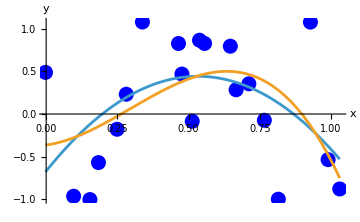

```mathematica
Show[Gdata2,GPol2]
```

```mathematica
(* Residuals, Error. Discuss   *)
```

```mathematica
Abs[p2["FitResiduals"]]
```

{1.16806,0.534368,0.660749,0.882876,0.7858,0.305482,0.0376807,0.0388674,0.423348,0.403147,0.52618,0.387539,0.404058,0.0378633,0.0870616,0.301964,1.24792,1.12871,0.349174,0.157718}

```mathematica
Res[p_]:=Abs[p["FitResiduals"]]
```

```mathematica
Lendata2=Dimensions[data2][[1]];
```

```mathematica
Ep2=Res[p2]
```

{1.16806,0.534368,0.660749,0.882876,0.7858,0.305482,0.0376807,0.0388674,0.423348,0.403147,0.52618,0.387539,0.404058,0.0378633,0.0870616,0.301964,1.24792,1.12871,0.349174,0.157718}

```mathematica
LSE[E_]:=Sqrt[Sum[E[[i]]^2,{i,Length[E]}]]
```

```mathematica
(* The LSE Error *)
```

```mathematica
LSE[Ep2]
```

2.75501

```mathematica
(* Modules: Program a Module input N=deg(p) data. Output p[x], Error, plot of the curve vs the data. 
The module uses functions Res[p] and LSE[EP] defined above  *)
```

```mathematica
PolFit[N_,data_]:=Module[{p,ER,basis,i,x,EP,plotdata,plotcurve,show,D1,xmin,xmax},basis=Table[x^i,{i,N}];p=LinearModelFit[data,basis,x];EP=Res[p];ER=LSE[EP];
D1=Transpose[data][[1]];
xmin=Min[D1];
xmax=Max[D1];
plotdata:=ListPlot[data,PlotStyle->{Red,PointSize[0.03]}];
plotcurve:=Plot[p[x],{x,xmin,xmax},PlotStyle->Blue];
show:=Show[plotdata,plotcurve];
{ER,p[x1],show}]
```

```mathematica
(* Note: the variable x1 is used for the output. The local variable x can be used as well *)
```

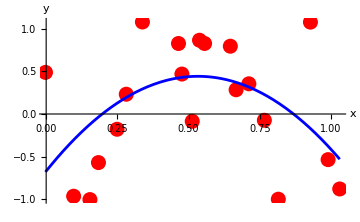
{2.75501,-0.670232+4.17593 x1-3.91989 x1^2,-Graphics-}

```mathematica
PolFit[2,data2]
```

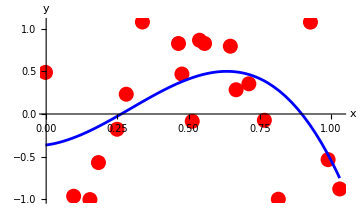
{2.68997,-0.363815+0.449333 x1+5.02424 x1^2-5.65248 x1^3,-Graphics-}

```mathematica
PolFit[3,data2]
```

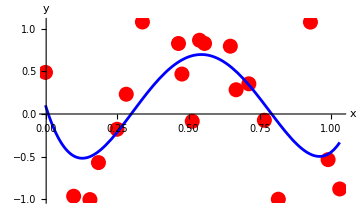
{2.43196,0.0769097-10.6346 x1+57.2198 x1^2-87.2039 x1^3+40.0935 x1^4,-Graphics-}

```mathematica
PolFit[4,data2]
```

```mathematica
(* Discuss the results   *)
```

```mathematica
(* Consider the trigonometric system {Sin[2Pi i x/N], Cos[2Pi i x/N]} *)
```

```mathematica
(* The basis consists of 4 functions NT=2*)
```

```mathematica
NT=2
```

2

```mathematica
Triglist=Table[{Sin[2*Pi*x*i/20],Cos[2*Pi*x*i/20]},{i,1,NT}]
```

{{Sin[(π x)/10],Cos[(π x)/10]},{Sin[(π x)/5],Cos[(π x)/5]}}

```mathematica
(* Delete internal brackets *)
```

```mathematica
Triglist=Flatten[Triglist,1]
```

{Sin[(π x)/10],Cos[(π x)/10],Sin[(π x)/5],Cos[(π x)/5]}

```mathematica
(* LS fit *)
```

```mathematica
TrigF=LinearModelFit[data2,Triglist,x];
```

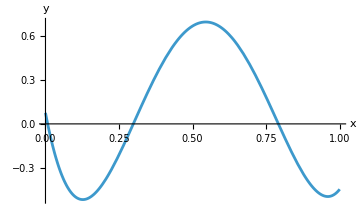

```mathematica
GTrigPol=Plot[TrigF[x],{x,0,1}]
```

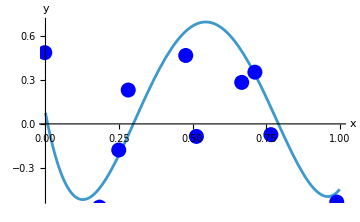

```mathematica
Show[GTrigPol,Gdata2]
```

```mathematica
ETrig=Res[TrigF];
```

```mathematica
LSE[ETrig]
```

2.43233

```mathematica
(* Yourself: write a module to approximate a data using the trigonometric system having 2*NT basis functions  *)
```

```mathematica
(* Approximate a space curve based on a synthetic data given by  data3. If time allows   *)
```

```mathematica
data3=Table[{Sin[t],Cos[t],t},{t,1.,10}]
```

{{0.841471,0.540302,1.},{0.909297,-0.416147,2.},{0.14112,-0.989992,3.},{-0.756802,-0.653644,4.},{-0.958924,0.283662,5.},{-0.279415,0.96017,6.},{0.656987,0.753902,7.},{0.989358,-0.1455,8.},{0.412118,-0.91113,9.},{-0.544021,-0.839072,10.}}

```mathematica
(* Length *)
```

```mathematica
L3=Dimensions[data3][[1]]
```

10

```mathematica
MatrixForm[data3]
```

(0.841471 | 0.540302 | 1.
0.909297 | -0.416147 | 2.
0.14112 | -0.989992 | 3.
-0.756802 | -0.653644 | 4.
-0.958924 | 0.283662 | 5.
-0.279415 | 0.96017 | 6.
0.656987 | 0.753902 | 7.
0.989358 | -0.1455 | 8.
0.412118 | -0.91113 | 9.
-0.544021 | -0.839072 | 10.)

```mathematica
(* Use parametric approximation  *)
```

```mathematica
x3=Transpose[data3][[1]]
```

{0.841471,0.909297,0.14112,-0.756802,-0.958924,-0.279415,0.656987,0.989358,0.412118,-0.544021}

```mathematica
y3=Transpose[data3][[2]]
```

{0.540302,-0.416147,-0.989992,-0.653644,0.283662,0.96017,0.753902,-0.1455,-0.91113,-0.839072}

```mathematica
z3=Transpose[data3][[3]]
```

{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}

```mathematica
(* Consider the mix of the trig basis and a linear function *)
```

```mathematica
Clear[t]
```

```mathematica
BS3={Sin[t],Cos[1.2t],t};
```

```mathematica
LMF3[x_]:=LinearModelFit[x,BS3,t]
```

```mathematica
{Sx3=LMF3[x3],Sy3=LMF3[y3],Sz3=LMF3[z3]}
```

{FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
S3[t_]:={Sx3[t],Sy3[t],Sz3[t]}
```

```mathematica
(* Check  *)
```

```mathematica
S3[t]
```

{0.+8.52989×10^-19 t-1.14139×10^-16 Cos[1.2 t]+1. Sin[t],0.0299348-0.0407094 t+0.75773 Cos[1.2 t]+0.622544 Sin[t],3.78382×10^-17+1. t-3.89129×10^-16 Cos[1.2 t]-4.60855×10^-16 Sin[t]}

```mathematica
(* Simplify *)
```

```mathematica
Chop[N[S3[t]]]
```

{1. Sin[t],0.0299348-0.0407094 t+0.75773 Cos[1.2 t]+0.622544 Sin[t],1. t}

```mathematica
GPol3=ParametricPlot3D[S3[t],{t,1,L3},BoxRatios->1]
```

-Graphics3D-

```mathematica
GData3=ListPointPlot3D[data3,PlotStyle->{PointSize[0.05],Blue}]
```

-Graphics3D-

```mathematica
ShowAll=Show[{GPol3,GData3},PlotRange->Full,BoxRatios->1]
```

-Graphics3D-

```mathematica
(* Approximation requires "good" basis functions or/and a relatively simple shape. 
When it is successful, it beats interpolation since it produces 
a closed form solution *)
```